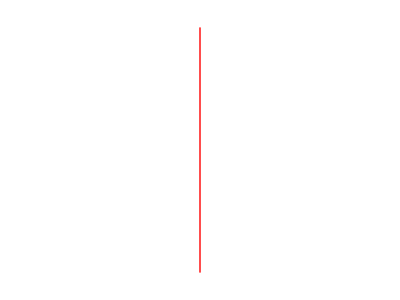

```mathematica
Graphics[{Red,Thick,Line[{{2,-5},{2,5}}]}]
```

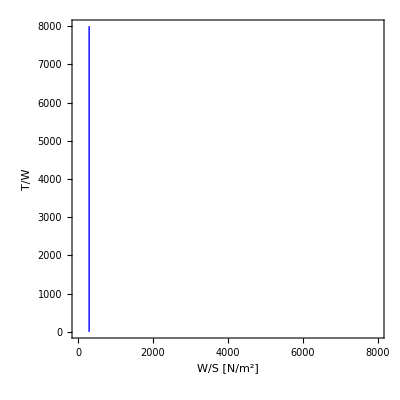

```mathematica
pluto=ContourPlot[x==297,{x,0,8000},{y,0,8000},ContourStyle->{Blue,Thick},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"],Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"}]
```

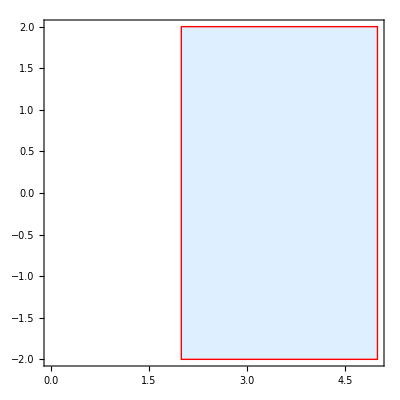

```mathematica
RegionPlot[x>2,{x,0,5},{y,-2,2},PlotStyle->LightBlue,BoundaryStyle->{Thick,Red}]
```

```mathematica
ContourPlot[x>2,{x,0,5},{y,-2,2},ContourStyle->None,PlotStyle->LightBlue,BoundaryStyle->{Thick,Red}]
```

-Graphics-

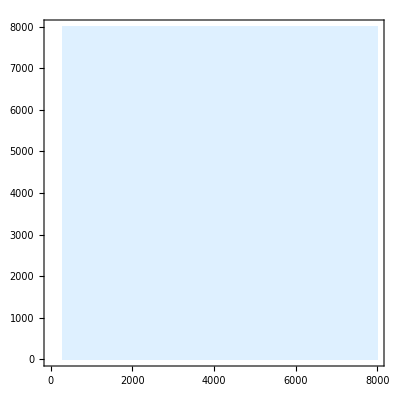

```mathematica
pippo=RegionPlot[x>297,{x,0,8000},{y,0,8000},PlotStyle->LightBlue,BoundaryStyle->None]
```

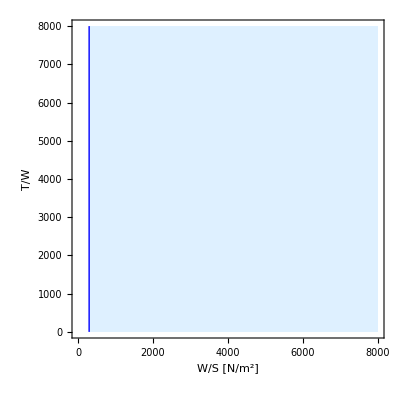

```mathematica
paperino=Show[pippo,pluto,Frame->True,FrameLabel->{"W/S [N/m^2]","T/W"},FrameStyle->Directive[Black,FontSize->16,FontFamily->"Arial"]]
```